```mathematica
nccpdf[x_,k_,λ_]:=1/2 ⅇ^(-(x+λ)/2) (x/λ)^(k/4-1/2) BesselI[k/2-1,√(λ x)]
```

```mathematica
Simplify[D[nccpdf[x,k,λ],x]]
```

1/(8 (x λ)^(3/2))ⅇ^(1/2 (-x-λ)) (x/λ)^(1/4 (-2+k)) λ (x λ BesselI[-2+k/2,√(x λ)]+(-2+k-2 x) √(x λ) BesselI[-1+k/2,√(x λ)]+x λ BesselI[k/2,√(x λ)])

```mathematica
Simplify[D[nccpdf[x,k,λ],x],k>2&&x>0&&λ>0]
```

1/(8 x^2)ⅇ^(1/2 (-x-λ)) (x/λ)^(k/4) (x λ BesselI[1/2 (-4+k),√(x λ)]+(-2+k-2 x) √(x λ) BesselI[1/2 (-2+k),√(x λ)]+x λ BesselI[k/2,√(x λ)])

```mathematica
FullSimplify[D[nccpdf[x,k,λ],x],k>2&&x>0&&λ>0]
```

1/4 ⅇ^(1/2 (-x-λ)) (x/λ)^(1/4 (-4+k)) (((-2+k-x) BesselI[1/2 (-2+k),√(x λ)])/(√(x λ))+BesselI[k/2,√(x λ)])

```mathematica
Solve[1/4 ⅇ^(1/2 (-x-λ)) (x/λ)^(1/4 (-4+k)) (((-2+k-x) BesselI[1/2 (-2+k),√(x λ)])/(√(x λ))+BesselI[k/2,√(x λ)])==0&&k>2&&x>0&&λ>0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/4 ⅇ^(1/2 (-x-λ)) (x/λ)^(1/4 (-4+k)) (((-2+k-x) BesselI[1/2 (-2+k),√(x λ)])/(√(x λ))+BesselI[k/2,√(x λ)])==0&&k>2&&x>0&&λ>0,x]

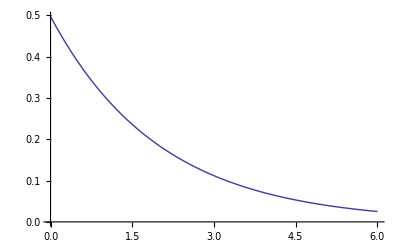

```mathematica
Plot[nccpdf[x,2,0.01],{x,0,6}]
```

```mathematica
cpdf[x_,k_]:=(x^(k/2-1) Exp[-x/2])/(2^(k/2) Gamma[k/2])
```

```mathematica
FullSimplify[cpdf[k-2,k],k>2]
```

((2 ⅇ)^(1-k/2) (-2+k)^(-2+k/2))/Gamma[-1+k/2]

```mathematica
D[cpdf[x,k],x]
```

(2^(-k/2) ⅇ^(-x/2) (-1+k/2) x^(-2+k/2))/Gamma[k/2]-(2^(-1-k/2) ⅇ^(-x/2) x^(-1+k/2))/Gamma[k/2]

```mathematica
Solve[2^(-k/2) ⅇ^(-x/2) (-1+k/2) x^(-2+k/2)-2^(-1-k/2) ⅇ^(-x/2) x^(-1+k/2)==0&&k>20,x]
```

{{x→ConditionalExpression[0,k>20]},{x→ConditionalExpression[-2+k,k>20]}}

```mathematica
N[cpdf[19,21]]
```

0.064152

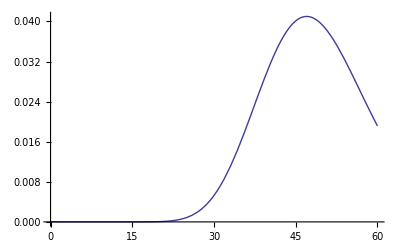

```mathematica
Plot[cpdf[x,49],{x,0,60}]
```